```mathematica
LanguageIdentify["ajatella"]
```

Finnish

```mathematica
tiger  = LinguisticAssistant
```

-Graphics-

```mathematica
ImageIdentify[tiger]
```

tiger

```mathematica
Table[ImageIdentify[Blur[tiger,r]],{r,1,5,1}]
```

{tiger,tiger,tiger,spiny-finned fish,fish}

```mathematica
Classify["Sentiment","I am so happy to be here"]
```

Positive

```mathematica
Nearest[WordList[],"happy",10]
```

{happy,haply,harpy,nappy,sappy,apply,campy,choppy,guppy,hairy}

```mathematica
Nearest[Table[RandomInteger[1000],20],100,3]
```

{138,143,53}

```mathematica
Nearest[RandomColor[10],Red,2]
```

{RGBColor[0.9183988949145341, 0.4299702169159796, 0.23689333387718858],RGBColor[0.4476519706191302, 0.2324030518055431, 0.009504927080394188]}

```mathematica
Nearest[Table[n^2,{n,100}],2000,1]
```

{2025}

```mathematica
flags = LinguisticAssistant;
```

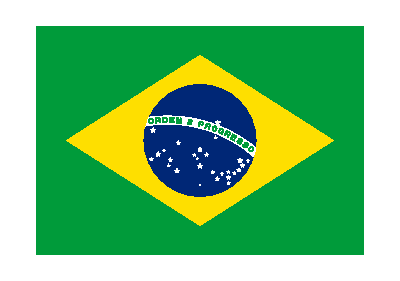

```mathematica
flagOfBrazil = LinguisticAssistant
```

```mathematica
Nearest[flags,flagOfBrazil,3]
```

{-Graphics-,-Graphics-,-Graphics-}

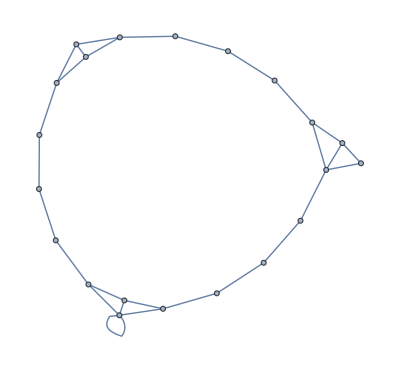

```mathematica
NearestNeighborGraph[Table[Hue[h],{h,0,1,0.05}],2,VertexLabels->All]
```

```mathematica
flagsOfAsians = LinguisticAssistant;
```

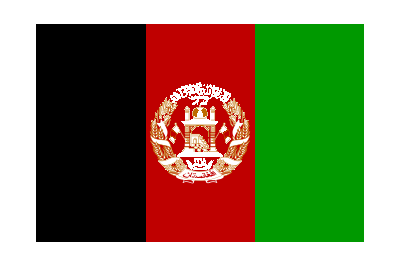
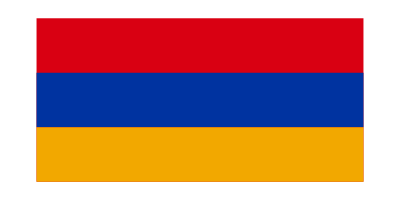
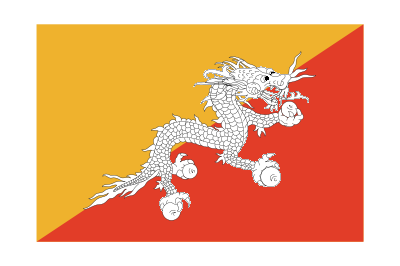

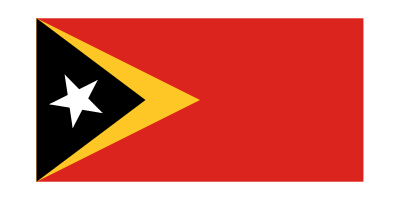
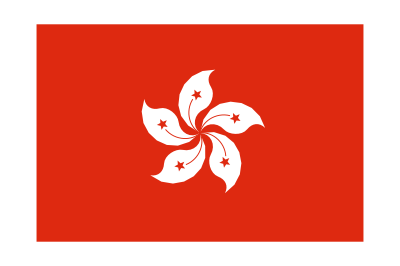
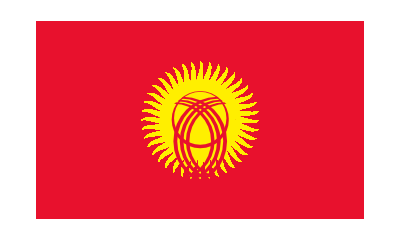
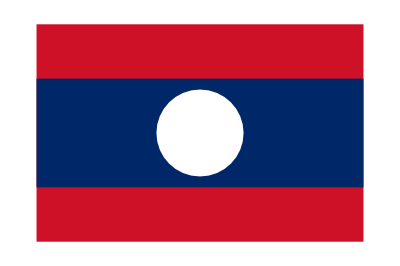
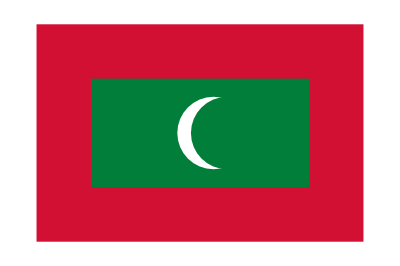

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-}}

```mathematica
FindClusters[flagsOfAsians]
```

```mathematica
alph = Table[Rasterize[Style[FromLetterNumber[n],20]],{n,26}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
NearestNeighborGraph[alph,2,VertexLabels->All]
```

-Graphics-

```mathematica
Table[Blur[Rasterize[Style["Hello",50]],r],{r,1,10}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
TextRecognize[Table[Blur[Rasterize[Style["Hello",50]],r],{r,1,10}]]
```

{Hello,Hello,Hello,Hello,Hello,Hello,Hello,Mono,hal lo,NH.}

```mathematica
Dendrogram[Table[Rasterize[FromLetterNumber[n]],{n,10}]]
```

-Graphics-

```mathematica
Table[Rasterize[ToUpperCase[FromLetterNumber[n]]],{n,26}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
FeatureSpacePlot[Table[Rasterize[ToUpperCase[FromLetterNumber[n]]],{n,26}]]
```

-Graphics-

```mathematica
Table[Blur[LinguisticAssistant,r],{r,1,5}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ImageIdentify[Table[Blur[LinguisticAssistant,r],{r,1,5}]]
```

{Eiffel Tower,Eiffel Tower,tower,stupa,stupa}

```mathematica
Classify["Sentiment",WikipediaData["happiness"]]
```

Neutral

```mathematica
Nearest[Table[Hue[h],{h,0,1,.05}],Pink,3]
```

{Hue[0.9500000000000001],Hue[0.9],Hue[0.05]}

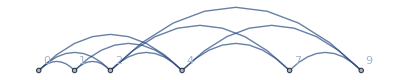

```mathematica
NearestNeighborGraph[Table[RandomInteger[10],10],3,VertexLabels->All]
```

```mathematica
FindClusters[RandomColor[100]]
```

{{RGBColor[0.057559653604312144, 0.5665973725871618, 0.20630122961459652],RGBColor[0.15288791455213846, 0.6938070830627299, 0.5095345676430079],RGBColor[0.18174061983152168, 0.5538526103025416, 0.030609290631196995],RGBColor[0.2255043531290568, 0.7751754082681912, 0.6588790215330063],RGBColor[0.22524050245217442, 0.6710694161249107, 0.5968755211481926],RGBColor[0.0001458355353414209, 0.7128952408346103, 0.5483200000923605],RGBColor[0.07297511762673103, 0.9886370325676319, 0.938335196025144],RGBColor[0.3913026299625957, 0.6687790399083802, 0.3076348758008305],RGBColor[0.3273863842550828, 0.6996605718032343, 0.3171443281639694],RGBColor[0.5739018020160322, 0.9928639030296533, 0.6302170329378731],RGBColor[0.2598475027942735, 0.8196989349546786, 0.7070897879503353],RGBColor[0.6005489457654205, 0.8371436157285539, 0.6466613774405712],RGBColor[0.044496493556982486, 0.5164755701436847, 0.08276943235161927]},{RGBColor[0.9341580707244597, 0.33435340438806915, 0.3151877206172393],RGBColor[0.9691783836073682, 0.35517517342556815, 0.31985122762816953],RGBColor[0.718064075046337, 0.5688709013810025, 0.8713053865979932],RGBColor[0.4156730170460541, 0.23068645098421525, 0.9157845854937579],RGBColor[0.5696748259950657, 0.13210209796439187, 0.7873504225305026],RGBColor[0.8665301929954079, 0.4344556488714102, 0.22243002257578137],RGBColor[0.4499787877443475, 0.3230962301491722, 0.15330766584874422],RGBColor[0.8677661778093766, 0.6190674890925381, 0.6975965650652018],RGBColor[0.8765859329474361, 0.5336644003954338, 0.6200636030800264],RGBColor[0.6803276441470529, 0.6086200197375002, 0.6577385476680744],RGBColor[0.16891647522534048, 0.2364909600149232, 0.7273545738522491],RGBColor[0.936340575155447, 0.34081595295636435, 0.564786248906789],RGBColor[0.7518797945061284, 0.6766433632997311, 0.8244999009414382],RGBColor[0.5943954365907786, 0.18786346033063972, 0.8287465213504106],RGBColor[0.15574126982791592, 0.18994458175701912, 0.9731087308717283],RGBColor[0.14445138523305157, 0.3100374478516368, 0.8892594809915555],RGBColor[0.10105439731784216, 0.14254149649381453, 0.8053674177928798],RGBColor[0.5998576496328034, 0.11465079925370558, 0.5536450779027471],RGBColor[0.9390691273404614, 0.5225223024168237, 0.4409162028904161],RGBColor[0.7026316059824731, 0.5796209895240643, 0.39320662640180215],RGBColor[0.5725770875683089, 0.5302054440885602, 0.4513132907299535],RGBColor[0.8853173781759784, 0.9981616674465204, 0.9788188283232666],RGBColor[0.12265668129632523, 0.05870515472549509, 0.8965845380262032],RGBColor[0.9397202096106476, 0.2809275657413097, 0.05115622012154053],RGBColor[0.2694702026511706, 0.13374503917197278, 0.26647367720062687],RGBColor[0.7936733245292142, 0.2003235977000133, 0.8972324028205956],RGBColor[0.4472687595521567, 0.29502565244252166, 0.9257917317218252],RGBColor[0.7821073490063031, 0.6091773114704699, 0.47699007251492564],RGBColor[0.6118855373715713, 0.6985159389187632, 0.8295317984872299],RGBColor[0.6264419198550282, 0.27882689054226995, 0.4693659486144577],RGBColor[0.8382227739419965, 0.07896029213871136, 0.0365821718926751],RGBColor[0.0040325161798588915, 0.12245860520219343, 0.5290921120123737],RGBColor[0.9529434992254031, 0.42149966058421584, 0.11381311200931865],RGBColor[0.8298852553425338, 0.49713092122764757, 0.959067431194252],RGBColor[0.9333369908344498, 0.2814068980059514, 0.2916873431268332],RGBColor[0.9400667505443185, 0.38077725138904817, 0.031121896160896334],RGBColor[0.9126189974239611, 0.8493603302278965, 0.9778763183747488],RGBColor[0.7115690463142312, 0.5658165648531148, 0.39701154757949375],RGBColor[0.37209291532262023, 0.5042423854785303, 0.9777305664992726],RGBColor[0.969710844131207, 0.2853857187591715, 0.14041426732945528],RGBColor[0.9677213589052573, 0.25797522981320253, 0.1512284080101498],RGBColor[0.9321110052160675, 0.42720107577926436, 0.5193629919424823]},{RGBColor[0.9657329084178499, 0.09785289416507403, 0.7068341538894527],RGBColor[0.915647299613259, 0.017101617961427618, 0.6995921532890346],RGBColor[0.9077753249824234, 0.05468557883470826, 0.7087453421833705],RGBColor[0.9638478825903105, 0.3137987998393954, 0.6256268240531877]},{RGBColor[0.35692628205510957, 0.3306607959570411, 0.43779284334857094],RGBColor[0.1417110738994405, 0.7348917596011573, 0.8422625005932602],RGBColor[0.10540189517886511, 0.6367876865652806, 0.6427678231365193],RGBColor[0.2610886876773961, 0.5602875992782177, 0.7077680230567809],RGBColor[0.08565771166742087, 0.5853791893159945, 0.6607665092524508],RGBColor[0.23660580928856856, 0.6346598987076231, 0.9863202697242124],RGBColor[0.13718108773329485, 0.05384583137722676, 0.2354712042344318],RGBColor[0.5020314652972211, 0.7197037826945551, 0.8669141789409887],RGBColor[0.1662628977825653, 0.4811501780276368, 0.8034908906532592],RGBColor[0.03147600459242206, 0.3455692936857375, 0.4909629651428997],RGBColor[0.03844854142701459, 0.16800641076371492, 0.46427046994194154],RGBColor[0.25761432939778395, 0.5907916364057748, 0.7444885423937013],RGBColor[0.46822170690026543, 0.6857510197500631, 0.9016746234863009],RGBColor[0.07638115997200634, 0.3383805947618086, 0.42354706892157123],RGBColor[0.38733937601165946, 0.5572181729553654, 0.9451944292934675],RGBColor[0.14920191936733085, 0.3055921163778421, 0.5613784399167876]},{RGBColor[0.9092203012656661, 0.5804758817444795, 0.053263855921779735],RGBColor[0.7912817977880027, 0.7771041280936914, 0.44754967117670397],RGBColor[0.8947344801444939, 0.9095783882199953, 0.4586442759092437],RGBColor[0.9854940722379015, 0.8986435915122337, 0.19313747342751153],RGBColor[0.823900869224393, 0.7983539079485926, 0.28145141991461253],RGBColor[0.6330333913340966, 0.6050345018989018, 0.17404980990802876],RGBColor[0.8720032089942593, 0.9484856081213069, 0.05410386045160753],RGBColor[0.9748484634689527, 0.795094631802113, 0.27127842872104635],RGBColor[0.718362498753591, 0.6718173741033615, 0.135715809149215],RGBColor[0.9274623942254347, 0.7559569653803087, 0.3198672481224354]},{RGBColor[0.12042155423900347, 0.8262982579413167, 0.1595426845873631],RGBColor[0.11010342319786726, 0.8717575194986182, 0.27735878444855655],RGBColor[0.17831934841928776, 0.8037132975708987, 0.22012930042667755],RGBColor[0.7501035238990796, 0.9296789539283294, 0.263665604783637],RGBColor[0.15423712135425793, 0.8175750306723291, 0.0991586672631819],RGBColor[0.5438424102705788, 0.9423233734331751, 0.03343618535680859],RGBColor[0.3707677510709031, 0.9264775303669748, 0.31950373074562366],RGBColor[0.18763584700378422, 0.8264155086691245, 0.12413092691536276],RGBColor[0.4438472825682789, 0.9455410269242006, 0.03198753015246458],RGBColor[0.5302022845051726, 0.9759592214434967, 0.5226154117179782],RGBColor[0.37921319190079417, 0.9933337714773804, 0.39101901626237323]},{RGBColor[0.35352077930946124, 0.026353397616396546, 0.14009107867259907],RGBColor[0.5381385913183283, 0.22372091638094038, 0.21006730016564767]},{RGBColor[0.19039557025490295, 0.2761747677369033, 0.010585528492374152],RGBColor[0.08833659048039144, 0.18872749095739816, 0.08914514935272622]}}

```mathematica
Table[Rasterize[FromLetterNumber[n]],{n,26}]
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
FeatureSpacePlot[Join[Table[Rasterize[FromLetterNumber[n]],{n,26}],Table[Rasterize[ToUpperCase[FromLetterNumber[n]]],{n,26}]]]
```

-Graphics-